```mathematica
$LifeData=Append[$LifeData,Select[lifeData,#Year>2023&]];
Length[$LifeData]
```

1393

```mathematica
discoveriesbyclass = ;
```

[[ Make a version where the bars are colored according to whether the new structure is actually “progress” ]]

#### Hist V2

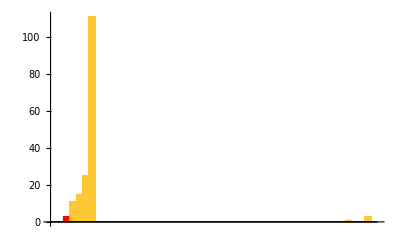
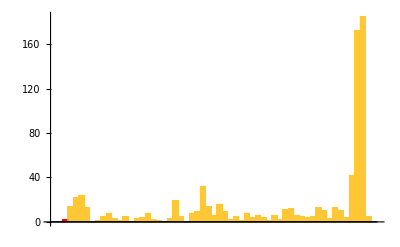
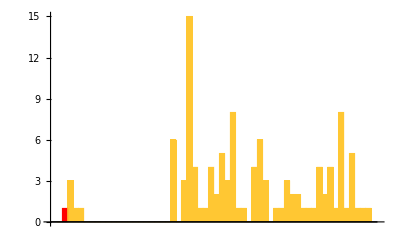
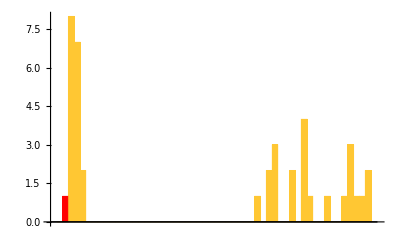
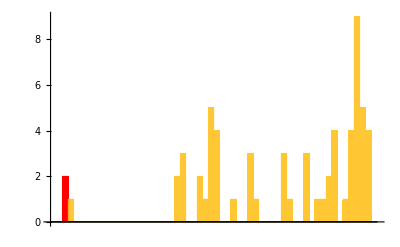
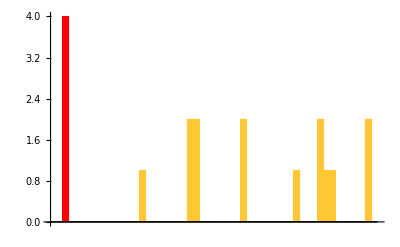
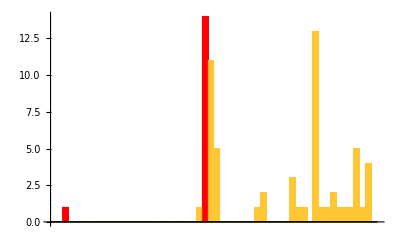
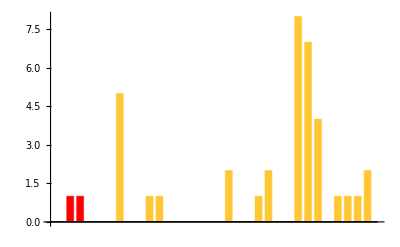

```mathematica
Function[class, 
Module[{}, weightsovertime = Select[SortBy[Select[Values[$LifeData],#Class===class&],#Year&][[All, "InitialWeight"]], IntegerQ];improvements = FoldList[Function[{min, next},If[next<min, next, min]],Infinity,  weightsovertime];

years = Sort[Select[Values[$LifeData],(#Class===class&)][[All, "Year"]]];
allyears = Table[i , {i, Range[First[years], Last[years]] }] ;locs = Select[Partition[improvements, 2, 1],#[[1]] != #[[2]]&-> "Index"];
BarChart[MapAt[Style[#, Red]&, BinCounts[Sort[Select[Values[$LifeData],(#Class===class&)][[All, "Year"]]], {1}], List[Lookup[Association[Thread[allyears-> Range[Last[years] - First[years] + 1]]], #]]&/@ years[[locs]] + 1]]


]]/@ Keys[Select[discoveriesbyclass,Length[#]>15&]]
```

#### By initial weight

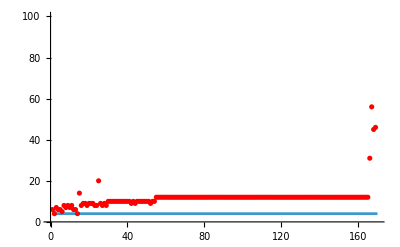
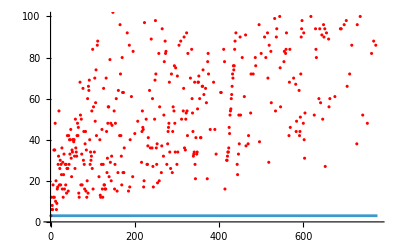
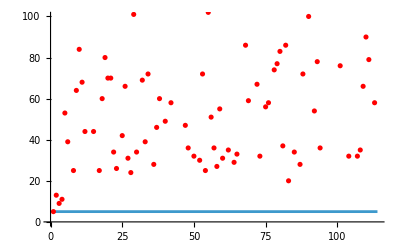
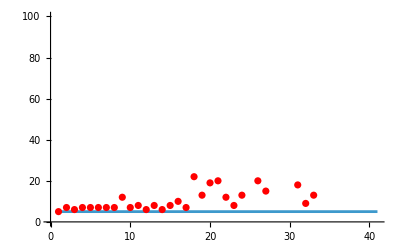
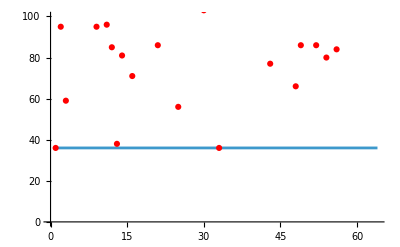
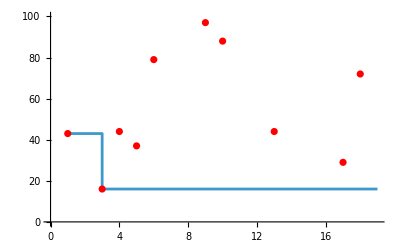
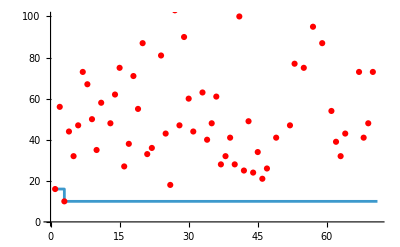
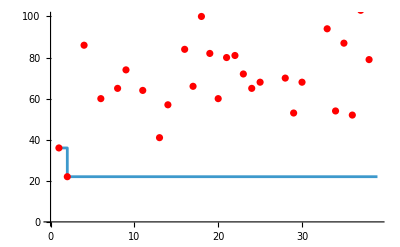
{-Graphics-Strict still life,-Graphics-Oscillator,-Graphics-Spaceship,-Graphics-Methuselah,-Graphics-Gun,-Graphics-Puffer,-Graphics-Conduit,-Graphics-Reflector}

```mathematica
Function[class, 
Module[{},
weightsovertime = Select[SortBy[Select[Values[$LifeData],#Class===class&],#Year&][[All, "InitialWeight"]], IntegerQ];
improvements = Rest[FoldList[Function[{min, next},If[next<min, next, min]],Infinity,  weightsovertime]] ;
Labeled[Show[ListStepPlot[improvements, PlotRange->100], ListPlot[weightsovertime, PlotStyle-> Red, PlotRange->100]], class]]]/@Keys[Select[discoveriesbyclass,Length[#]>15&]]
```

#### By area of bounding box

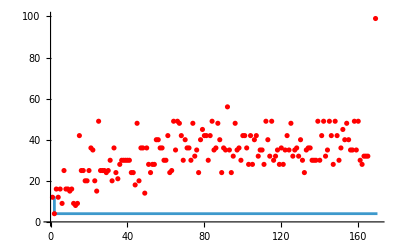
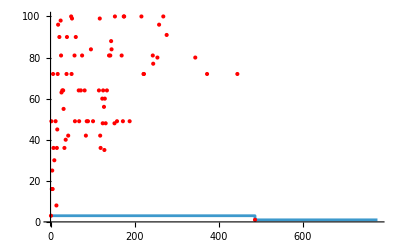
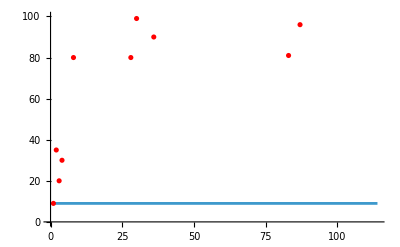
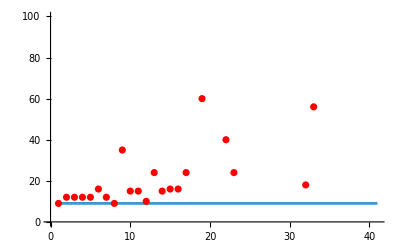
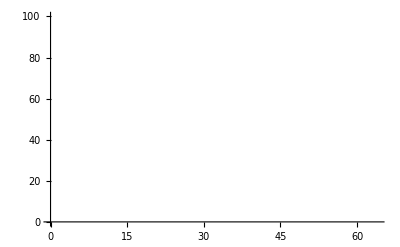
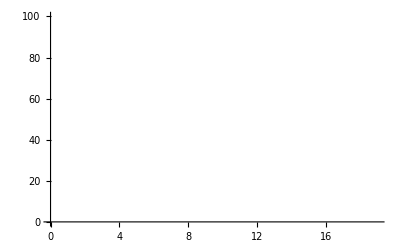
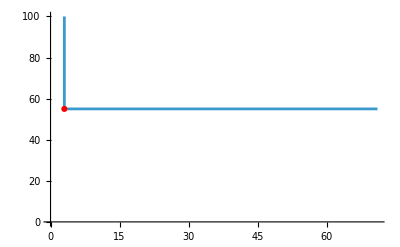
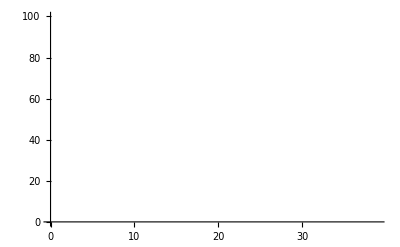
{-Graphics-Strict still life,-Graphics-Oscillator,-Graphics-Spaceship,-Graphics-Methuselah,-Graphics-Gun,-Graphics-Puffer,-Graphics-Conduit,-Graphics-Reflector}

```mathematica
Function[class, 
Module[{},
weightsovertime = Select[If[KeyExistsQ[#, "MatrixData"], Times@@Dimensions[#MatrixData], -1]&/@SortBy[Select[Values[$LifeData],#Class===class&],#Year&], Positive[#]&];
improvements = Rest[FoldList[Function[{min, next},If[next<min, next, min]],Infinity,  weightsovertime]] ;
Labeled[Show[ListStepPlot[improvements, PlotRange->100], ListPlot[weightsovertime, PlotStyle-> Red, PlotRange->100] ], class]]]/@Keys[Select[discoveriesbyclass,Length[#]>15&]]
```

#### Progressive Decrease for Constant Period

```mathematica
Transpose[Table[Map[Labeled[ArrayPlot[#MatrixData,ImageSize->20 Sqrt[Dimensions[#MatrixData]]],{#Year,#Period}]&,SortBy[First/@Map[MinimalBy[#,#[tt]&]&,Values@GroupBy[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period&]],#Period&]],{tt,{"Year","InitialWeight"}}]]
```

ArrayPlot::mat: Argument $Failed at position 1 is not a list of lists.

$Aborted

```mathematica
Column/@Transpose[Table[Map[Labeled[ArrayPlot[#MatrixData,ImageSize->20 Sqrt[Dimensions[#MatrixData]]],{#Year,#Period}]&,SortBy[First/@Map[MinimalBy[#,#[tt]&]&,Values@GroupBy[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period&]],#Period&]],{tt,{"Year","InitialWeight"}}]]
```

```mathematica
SortBy[Select[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&], #Period == 3&], #Year&][[All, "InitialWeight"]]
```

{18,48,28,54,18,30,33,144,14,26,26,40,40,45,31,22,40,32,36,46,18,18,60,16,22,13,16,12,28,65,16,16,70,48,29,48,144,60,24,190,258,19,140,21,33,33,30}

```mathematica
weightsovertime = SortBy[Select[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&], #Period == 3&], #Year&][[All, "InitialWeight"]]
```

{18,48,28,54,18,30,33,144,14,26,26,40,40,45,31,22,40,32,36,46,18,18,60,16,22,13,16,12,28,65,16,16,70,48,29,48,144,60,24,190,258,19,140,21,33,33,30}

```mathematica
improvements = FoldList[Function[{min, next},If[next<min, next, min]],Infinity,  weightsovertime]
```

{∞,18,18,18,18,18,18,18,18,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,13,13,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12}

```mathematica
locs = Select[Partition[improvements, 2, 1],#[[1]] != #[[2]]&-> "Index"]
```

{1,9,26,28}

```mathematica
ArrayPlot[#MatrixData, ImageSize->6Last[Dimensions[#MatrixData]], Mesh->True]&/@ SortBy[Select[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&], #Period == 3&], #Year&][[locs]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}